```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
Get["filegrabber.m"]
```

```mathematica
getFilename["ProjectQ", 16, 10, 30]
```

Python/results/ARC_ProjectQ/threads16/depth10/qubits30.txt

```mathematica
Get[getFilename["ProjectQ", 16, 10, 30]]
```

<|platform→ARC,framework→ProjectQ,filename→results/ARC_ProjectQ/threads16/depth10/qubits30.txt,numThreads→16,circuitDepth→10,numQubits→30,numRepetitions→10,durations→{351.501,351.411,351.158,351.602,351.232,351.345,351.491,351.412,351.449,351.441},realMemories→{17217753088,17217773568,17217785856,17217798144,17217810432,17217822720,17217835008,17217847296,17217855488,17217855488},virtualMemories→{18276605952,18276605952,18276605952,18276605952,18276605952,18276605952,18276605952,18276605952,18276868096,18276868096},normErrors→{-6.13294×10^-11,8.79552×10^-12,-2.27529×10^-12,-1.99574×10^-11,9.30334×10^-12,-2.10076×10^-12,-6.00497×10^-12,-1.90448×10^-12,-6.51168×10^-12,4.07322×10^-11}|>

```mathematica
Get[getFilename["QuEST", 16, 10, 30]]
```

<|platform→ARC,framework→QuEST,filename→results/ARC_QuEST/threads16/depth10/qubits30.txt,numThreads→16,circuitDepth→10,numQubits→30,numRepetitions→10,randomSeed→15927612609277242709,durations→{71.8843,70.5821,70.9378,70.1798,70.2532,70.6238,70.2254,71.3527,71.3355,70.9521},normErrors→{1.15463×10^-14,1.11022×10^-14,1.16573×10^-14,1.15463×10^-14,1.14353×10^-14,1.13243×10^-14,1.09912×10^-14,1.14353×10^-14,1.17684×10^-14,1.14353×10^-14},currRealMemories→{16779420000,16779456000,16779456000,16779456000,16779456000,16779456000,16779456000,16779456000,16779456000,16779456000},peakRealMemories→{16779420000,16779456000,16779460000,16779460000,16779460000,16779460000,16779460000,16779460000,16779460000,16779460000},currVirtMemories→{16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000},peakVirtMemories→{16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000,16943948000}|>

## How QuEST and ProjectQ speedup over threads

```mathematica
With[
	{threadVals = {2, 4, 8, 16, 32}},
	Manipulate[
		ListLinePlot[{
			Transpose[{
				threadVals,
				Table[
					Mean @ Get[getFilename["instMode0_results", "ProjectQ", threads, circuitDepth, numQubits]]["durations"],
					{threads, threadVals}
				]
			}],
			Transpose[{
				threadVals,
				Table[
					Mean @ Get[getFilename["results", "QuEST", threads, circuitDepth, numQubits]]["durations"],
					{threads, threadVals}
				]
			}]},
			PlotStyle -> Dashed,
			PlotMarkers -> Automatic,
			AxesLabel -> {"number of threads", "runtime (s)"},
			PlotLegends -> Placed[{"ProjectQ", "QuEST"},Above]
		],
		{circuitDepth, 10, 100, 10},
		{numQubits, 2, 30, 1}
	]
]
```

Global`getFilename::shdw: Symbol getFilename appears in multiple contexts {Global`,fileGrabber`}; definitions in context Global` may shadow or be shadowed by other definitions.

## full-param-comparison of QuEST, ProjectQ

### gate_fusion=False (projectQ slow) and using intel gcc (QuEST imprecise)

```mathematica
With[
	{threadVals = {1, 2, 4, 8, 16, 32},
	qubitRange = Range[1,30]},
	Manipulate[
		With[
			{
				imsize = Medium,
				projectQDurs = N @ Table[Mean @ Get[getFilename["ProjectQ", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				questDurs = N @ Table[Mean @ Get[getFilename["QuEST", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				projectQDurSD = N @ Table[StandardDeviation @ Get[getFilename["ProjectQ", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				questDurSD = N @ Table[StandardDeviation @ Get[getFilename["QuEST", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				projectQMems = N @Table[Mean @ Get[getFilename["ProjectQ", numThreads, circuitDepth, numQubits]]["realMemories"], {numQubits, qubitRange}],
				questMems = N @ Table[Mean @ Get[getFilename["QuEST", numThreads, circuitDepth, numQubits]]["currRealMemories"], {numQubits, qubitRange}],
				projectQErrors = N @Table[Mean @ Get[getFilename["ProjectQ", numThreads, circuitDepth, numQubits]]["normErrors"], {numQubits, qubitRange}],
				questErrors = N @ Table[Mean @ Get[getFilename["QuEST", numThreads, circuitDepth, numQubits]]["normErrors"], {numQubits, qubitRange}]

			 },
			Grid[{
				{
					ListLogPlot[
						{Transpose[{qubitRange, projectQDurs}],
						Transpose[{qubitRange, questDurs}]},
						PlotStyle -> Dashed,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "runtime (s)"},
						Filling -> {1 -> {2}},
						PlotLegends -> Placed[{"ProjectQ", "QuEST"},Above],
						ImageSize -> imsize
						(* PlotLabel -> "Performance" *)
					],
					ListLogPlot[
						Transpose[{qubitRange, projectQDurs/questDurs}],
						PlotStyle -> {Dashed, Black},
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "runtime ratio"},
						ImageSize -> imsize,
						PlotLegends -> Placed[{"ProjectQ / QuEST"}, Above],
						GridLines -> {{}, {1, 4}}
					],
					ListLogPlot[
						{Transpose[{qubitRange, projectQDurSD}],
						Transpose[{qubitRange, questDurSD}]},
						PlotStyle -> Dashed,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "sd(runtime) (s)"},
						Filling -> {1 -> {2}},
						PlotLegends -> Placed[{"ProjectQ", "QuEST"},Above],
						ImageSize -> imsize,
						PlotLabel -> "standard deviation of runtime"
					],
				},
				{
					ListLogPlot[
						{Transpose[{qubitRange, projectQMems/10^9}],
						Transpose[{qubitRange, questMems/10^9}]},
						PlotStyle -> Dashed,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "memory (GB)"},
						Filling -> {1 -> {2}},
						ImageSize -> imsize,
						PlotLabel -> "Memory consumption (after allocation)"
					],
					ListLogPlot[
						Transpose[{qubitRange, projectQMems/questMems}],
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "memory ratio"},
						ImageSize -> imsize,
						PlotStyle -> {Dashed, Black},
						GridLines -> {{}, {1}}
					]
				},
				{
					ListLinePlot[
						{Transpose[{qubitRange, projectQErrors}],
						Transpose[{qubitRange, questErrors}]},
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "1 - |ψ|^2"},
						Filling -> {2 -> {1}},
						Joined -> False,
						ImageSize -> imsize,
						PlotRange -> {0, Automatic},
						PlotLabel -> "Normalisation Error"
					],
					ListLinePlot[
						Transpose[{qubitRange, projectQErrors/questErrors}],
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "error ratio"},
						Joined -> False,
						ImageSize -> imsize,
						PlotRange -> {0, Automatic},
						PlotStyle -> {Dashed, Black}
					]
				}}
			]
		],
		{{circuitDepth, 100}, 10, 100, 10},
		{{numThreads, 16}, threadVals},
		ContinuousAction -> False
	]
]
```

Get::stream: Global`getFilename[ProjectQ,16,100,1] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[ProjectQ,16,100,2] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[ProjectQ,16,100,3] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Get::stream will be suppressed during this calculation.

Get::stream: Global`getFilename[ProjectQ,16,100,1] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[ProjectQ,16,100,2] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[ProjectQ,16,100,3] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Get::stream will be suppressed during this calculation.

## Demo of ProjectQ (gate_fusion=False) 22qb growth

```mathematica
Manipulate[
	Grid[
		Partition[#, 3]& @
		Table[
			ListLogPlot[
				{
					Transpose[{Range[1,30], N @ Table[Mean @ Get[getFilename["ProjectQ", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, Range[1,30]}]}],
					Transpose[{Range[20,30], N @ Table[Mean @ Get[getFilename["QuEST", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, Range[20,30]}]}]
				},
				PlotLabel -> Style[StringJoin[ToString[numThreads], If[numThreads > 1, " threads", " thread"]], Switch[numThreads, 16, RGBColor[0., 0.5019607843137255, 0.25098039215686274], 32, Red, _, Black]],
				ImageSize -> Medium,
				Joined -> {False, True},
				PlotStyle -> {Dashed},
				AxesLabel -> If[numThreads===8, {"qubits", "runtime (s)"}]
			], 
			{numThreads, {1, 2, 4, 8, 16, 32}}
		]
	],
	{{circuitDepth, 100}, 10, 100, 10}
]
```

### number of caches required

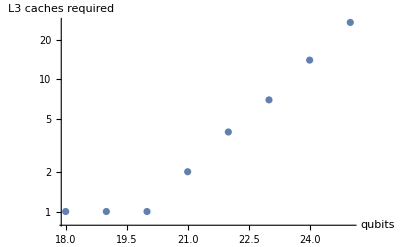

```mathematica
projectQReqMem[qb_] = 16 * 2^qb;
With[
	{cacheSize = 20480*1000, range=Range[18,25]},
	ListLogPlot[
		Transpose[{range, Ceiling[(projectQReqMem /@ range) / cacheSize]}],
		AxesLabel -> {"qubits", "L3 caches required"}
	]
]
```

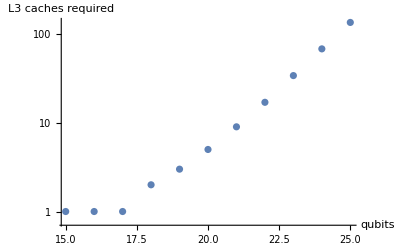

```mathematica
projectQReqMem[qb_] = 16 * 2^qb;
With[
	{cacheSize = 4000*1000, range=Range[15,25]},
	ListLogPlot[
		Transpose[{range, Ceiling[(projectQReqMem /@ range) / cacheSize]}],
		AxesLabel -> {"qubits", "L3 caches required"}
	]
]
```

## resim with gate_fusion=True runtime over threads, 15-30qb

```mathematica
getFilename["ProjectQ", 16, 100,10]
```

Python/results/ARC_ProjectQ/threads16/depth100/qubits10.txt

```mathematica
Manipulate[
With[
	{
		imsize = Medium,
		projectQDurs = N @ Table[Mean @ Get[
			getFilename["instMode5_results", "ProjectQ", numThreads, 100, numQubits]
			]["durations"], {numQubits, 15,30}],
		questDurs = N @ Table[Mean @ Get[getFilename["QuEST", numThreads, 100, numQubits]]["durations"], {numQubits, 15,30}]
	},
	Grid[{{
					ListLogPlot[
						{Transpose[{Range[15,30], projectQDurs}],
						Transpose[{Range[15,30], questDurs}]},
						PlotStyle -> Dashed,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "runtime (s)"},
						Filling -> {1 -> {2}},
						ImageSize -> imsize,
						PlotLegends -> Placed[{"ProjectQ", "QuEST"},Above]
					],
					ListLogPlot[
						Transpose[{Range[15,30], projectQDurs/questDurs}],
						PlotStyle -> Black,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "runtime (s)"},
						GridLines -> {{}, {1, 2}},
						ImageSize -> imsize
					]
	}}
	]
],
{{numThreads,16}, {1,2,4,8,16}}
]
```

Get::stream: Global`getFilename[instMode5_results,ProjectQ,16,100,15] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode5_results,ProjectQ,16,100,16] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode5_results,ProjectQ,16,100,17] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Get::stream will be suppressed during this calculation.

Get::stream: Global`getFilename[instMode5_results,ProjectQ,16,100,15] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode5_results,ProjectQ,16,100,16] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode5_results,ProjectQ,16,100,17] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Get::stream will be suppressed during this calculation.

## limited comparison of QuEST, ProjectQ

### gate_fusion=True, localopt=5 and using GNU gcc

```mathematica
With[
	{
		threadVals = {1, 16},
		circuitDepth = 100,
		pydir = "instMode6_results",
		cdir = "newgcc_results",
		qubitRange = Range[1,30]
	},
	Manipulate[
		With[
			{
				imsize = Medium,
				projectQDurs = N @ Table[Mean @ Get[getFilename[pydir, "ProjectQ", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				questDurs = N @ Table[Mean @ Get[getFilename[cdir, "QuEST", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				projectQDurSD = N @ Table[StandardDeviation @ Get[getFilename[pydir, "ProjectQ", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				questDurSD = N @ Table[StandardDeviation @ Get[getFilename[cdir, "QuEST", numThreads, circuitDepth, numQubits]]["durations"], {numQubits, qubitRange}],
				projectQMems = N @ Table[1000 * Mean @ Get[getFilename[pydir, "ProjectQ", numThreads, circuitDepth, numQubits]]["currRealMemories"], {numQubits, qubitRange}],
				questMems = N @ Table[Mean @ Get[getFilename[cdir, "QuEST", numThreads, circuitDepth, numQubits]]["currRealMemories"], {numQubits, qubitRange}],
				projectQErrors = N @Table[Mean @ Get[getFilename[pydir, "ProjectQ", numThreads, circuitDepth, numQubits]]["normErrors"], {numQubits, qubitRange}],
				questErrors = N @ Table[Mean @ Get[getFilename[cdir, "QuEST", numThreads, circuitDepth, numQubits]]["normErrors"], {numQubits, qubitRange}]
			 },
			Grid[{
				{
					ListLogPlot[
						{Transpose[{qubitRange, projectQDurs}],
						Transpose[{qubitRange, questDurs}]},
						PlotStyle -> Dashed,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "runtime (s)"},
						Filling -> {1 -> {2}},
						PlotLegends -> Placed[{"ProjectQ", "QuEST"},Above],
						ImageSize -> imsize
						(* PlotLabel -> "Performance" *)
					],
					ListLogPlot[
						Transpose[{qubitRange, projectQDurs/questDurs}],
						PlotStyle -> {Dashed, Black},
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "runtime ratio"},
						ImageSize -> imsize,
						PlotLegends -> Placed[{"ProjectQ / QuEST"}, Above],
						GridLines -> {{}, {1, 2}}
					],
					ListLogPlot[
						{Transpose[{qubitRange, projectQDurSD}],
						Transpose[{qubitRange, questDurSD}]},
						PlotStyle -> Dashed,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "sd(runtime) (s)"},
						Filling -> {1 -> {2}},
						PlotLegends -> Placed[{"ProjectQ", "QuEST"},Above],
						ImageSize -> imsize,
						PlotLabel -> "standard deviation of runtime"
					],
				},
				{
					ListLogPlot[
						{Transpose[{qubitRange, projectQMems/10^9}],
						Transpose[{qubitRange, questMems/10^9}]},
						PlotStyle -> Dashed,
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "memory (GB)"},
						Filling -> {1 -> {2}},
						ImageSize -> imsize,
						PlotLabel -> "Memory consumption (after allocation)"
					],
					ListLogPlot[
						Transpose[{qubitRange, projectQMems/questMems}],
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "memory ratio"},
						ImageSize -> imsize,
						PlotStyle -> {Dashed, Black},
						GridLines -> {{}, {1}}
					]
				},
				{
					ListLinePlot[
						{Transpose[{qubitRange, projectQErrors}],
						Transpose[{qubitRange, questErrors}]},
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "1 - |ψ|^2"},
						Filling -> {2 -> {1}},
						Joined -> False,
						ImageSize -> imsize,
						PlotRange -> {0, Automatic},
						PlotLabel -> "Normalisation Error"
					],
					ListLinePlot[
						Transpose[{qubitRange, projectQErrors/questErrors}],
						PlotMarkers -> Automatic,
						AxesLabel -> {"qubits", "error ratio"},
						Joined -> False,
						ImageSize -> imsize,
						PlotRange -> {0, Automatic},
						PlotStyle -> {Dashed, Black}
					]
				}}
			]
		],
		{{numThreads, 16}, threadVals},
		ContinuousAction -> False
	]
]
```

Get::noopen: Cannot open C/newgcc_results/ARC_QuEST/threads1/depth100/qubits26.txt.

Get::noopen: Cannot open C/newgcc_results/ARC_QuEST/threads1/depth100/qubits27.txt.

Get::noopen: Cannot open C/newgcc_results/ARC_QuEST/threads1/depth100/qubits28.txt.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,1] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,2] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,3] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Get::stream will be suppressed during this calculation.

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,1] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,2] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,3] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Get::stream will be suppressed during this calculation.

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,1] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,2] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Get::stream: Global`getFilename[instMode6_results,ProjectQ,16,100,3] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Get::stream will be suppressed during this calculation.